Initializations

```mathematica
CreatePalette@Grid[{{Button["Hide Inputs",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Input",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->False,ShowCellBracket->False]]],Button["Show Inputs",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Input",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->True,ShowCellBracket->True]]]},{Button["Hide Output",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->False,ShowCellBracket->False]]],Button["Show Output",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->True,ShowCellBracket->True]]]},{Button["Hide Text",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Text",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->False,ShowCellBracket->False]]],Button["Show Text",Module[{nb},nb=SelectedNotebook[];
NotebookFind[SelectedNotebook[],"Text",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->True,ShowCellBracket->True]]]},{Button["Delete Output",Module[{nb},nb=SelectedNotebook[];
NotebookDelete@Cells[nb,CellStyle->"Output"||"Print"||"Echo"]]]},{Button["Clear variables",Module[{nb},nb=SelectedNotebook[];
Clear["Global`*"];]],Button["Remove variables",Module[{nb},nb=SelectedNotebook[];
Remove["Global`*"]]]}}];
```

```mathematica
Needs["Notation`"]
Needs["HaneeshPackages`"]
Needs["MaTeX`"]
Get[URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ToTerminal.wl"]]
```

```mathematica
Dynamic[Refresh[({#,Names[#]}&/@{"Global`*","Love`*","ComplexSymbols`*"})//TableForm[#,TableDirections->Row]&,UpdateInterval->1]]//ToTerminal
```

```mathematica
Symbolize[UnderBar[x_]]
```

```mathematica
Symbolize[Subscript[x_, _]]
```

```mathematica
Symbolize[(∂x_)/(∂y_)]
```

Hype-Graphics-

Title

CAREER: Engineering Plasticity and Fracture toughness through Bio-inspiration, Geometric Design, and  Digital Manufacturing.


 CAREER: Artificial, engineered, quasi-crystalline plasticity for the rational, bio-inspired mechanical design of 3D printed materials for enhancing fracture toughness and damage tolerance.
 
  CAREER: Artificially engineering  plasticity for the rational, bio-inspired mechanical design of 3D printed materials for enhancing fracture toughness


 /.;

```mathematica
Symbolize[UnderBar[x_]]
Symbolize[OverBar[x_]]
Symbolize[Subscript[x_, _]]
(*Symbolize[Subscript[x_, 2]]
Symbolize[Subscript[x_, 3]]
*)
```

```mathematica
ClearAll[ech]
SetAttributes[ech,HoldFirst]
ech[x_]:=Module[{},
Print[HoldForm[x], "= ",x//MatrixForm];
];




ClearAll[I̲,Subscript[n, sd]];
Ι̲=Table[KroneckerDelta[i,j],{i,1,3},{j,1,3}];
Ι̲//MatrixForm

Subscript[n, sd]=3;

ClearAll[x̲];
ClearAll[σ]
Format[σ[i_,j_]]:=Subscript[σ,ToString[i]<>ToString[j]]
Format[x[i_]]:=Subscript[x,ToString[i]]
Format[u[i_]]:=Subscript[u,ToString[i]]
σ[2,1][x__]:=σ[1,2][x];
σ[3,2][x__]:=σ[2,3][x];
σ[3,1][x__]:=σ[1,3][x];
σ[2,1]:=σ[1,2];
σ[3,2]:=σ[2,3];
σ[3,1]:=σ[1,3];

x̲:=Table[x[i],{i,1,3}];
x̲//MatrixForm


σEigenBasis[command_]:=
Module[{},

Block[{σ,x̲},

x̲={x[1],x[2],x[3]};
σ[2,1]:=σ[1,2];
σ[3,2]:=σ[2,3];
σ[3,1]:=σ[1,3];
σ[1,2]:=0;
σ[2,3]:=0;
σ[1,3]:=0;
σ[1,1]:=Subscript[σ, 1];
σ[2,2]:=Subscript[σ, 2];
σ[3,3]:=Subscript[σ, 3];
command


]
]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(x_1
x_2
x_3)

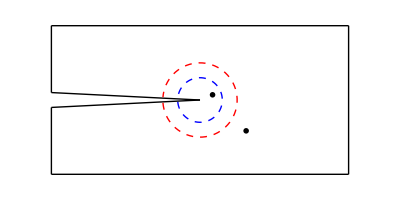

```mathematica
pt={0,0.1};
(*Manipulate[*)
Graphics[{Line[{pt,pt=pt+{0,.9}}],
Line[{pt,pt=pt+{4,0}}],
Line[{pt,pt=pt+{0,-2}}],
Line[{pt,pt=pt+{-4,0}}],
Line[{pt,pt=pt+{0,0.9}}],
Line[{pt,pt=pt+{2,0.1}}],
Line[{pt,pt=pt+{-2,0.1}}],
{Red,Dashed,Circle[{2,0},.5,{-3.06557,3.06557}]},
Text[MaTeX["\\color{red}{\\Gamma_{R}}",FontSize->10,"Preamble"->{"\\usepackage{color}"}],{2.621,-0.415}],
{Blue,Dashed,Circle[{2,0},.3,{-3.05646,3.05646}]},
Text[MaTeX["\\color{blue}{\\Gamma_{r}}",FontSize->8,"Preamble"->{"\\usepackage{color}"}],{2.169,0.07}]
},PlotRange->{{-0.2,4.2},{-1.1,1.1}}](*,{p,Locator}
]
*)
```

```mathematica
ClearAll[σ̲]
σ̲[x̲:_]:=Module[{Subscript[n, sd]=Length[x̲]},
Table[σ[i,j]@@x̲,{i,1,3},{j,1,3}]
]
σ̲[]:=Module[{Subscript[n, sd]=Length[x̲]},
Table[σ[i,j],{i,1,3},{j,1,3}]
]

σ̲[x̲]//pdConv//MatrixForm
σ̲[]//pdConv//MatrixForm
```

Mean, Stress Deviator, and .

```mathematica
Subscript[σ, m]:=1/3 Tr[σ̲[]];
s̲[]:=(σ̲[]-Subscript[σ, m] Ι̲)
Subscript[J, 2]:=1/2 Sum[s̲[][[i,j]]s̲[][[i,j]],{i,1,3},{j,1,3}]
```

The invariants of the second order tensor are: , , and 
 (1^st invariant)
 (2^nd invariant)
 ( 3rd invariant)

```mathematica
Subscript[Ι, 1][t_]:=
(∑_(i=1)^Subscript[n, sd] t⟦i,i⟧)

Subscript[Ι, 2][t_]:=1/2(
∑_(i=1)^Subscript[n, sd] ∑_(j=1)^Subscript[n, sd] t⟦i,j⟧t⟦i,j⟧-(∑_(i=1)^Subscript[n, sd] t⟦i,i⟧)(∑_(j=1)^Subscript[n, sd] t⟦j,j⟧)
)
Subscript[Ι, 3][t_]:=Det[t]

Subscript[Ι, 1][σ̲[]]
Subscript[Ι, 2][σ̲[]]//Simplify
Subscript[Ι, 3][σ̲[]]
```

, ,  eigen values or the principle values of the stress tensor.

```mathematica
σEigenBasis[Subscript[Ι, 1][σ̲[]]]
σEigenBasis[Subscript[Ι, 2][σ̲[]]//Simplify]
σEigenBasis[Subscript[Ι, 3][σ̲[]]//Simplify]
```

(mean stress or hydrostatic stress)
.

Plain Strain, strain in terms of displacement

```mathematica
Block[{u̲,ϵ̲,σ̲},
u̲[x̲:_]:=Flatten[{Table[u[i][x̲[[1]],x̲[[2]]],{i,1,2}],0}];
ϵ̲[x̲:_]:=1/2(Grad[u̲[x̲],x̲]+Grad[u̲[x̲],x̲]ᵀ);
ech[u̲[x̲]];
ech[ϵ̲[x̲]//pdConv];
0
];
```

J-integral example, infinite strip, Plane Strain

-Graphics-

```mathematica
Block[{u̲,ϵ̲,u,λ,μ},
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
u[2][x[2]]=(u x[2])/H;
u̲[x̲:_]:=Flatten[{0,Table[u[i][x̲[[2]]],{i,2,2}],0}];
ϵ̲[x̲:_]:=1/2(Grad[u̲[x̲],x̲]+Grad[u̲[x̲],x̲]ᵀ);
(2μ ϵ̲[x̲]+λ Tr[ ϵ̲[x̲]] Ι̲)//pdConv//TraditionalForm//MatrixForm;
ech[u̲[x̲]];
ech[ϵ̲[x̲]//pdConv];
σ̲[ϵ̲:_]:=
(2μ ϵ̲[x̲]+λ Tr[ ϵ̲[x̲]] Ι̲)//Simplify;
ech[σ̲[ϵ̲]//pdConv];
Echo[Div[σ̲[ϵ̲],x̲],"Div of stress"];
Echo[1/2 Flatten[σ̲[ϵ̲]].Flatten[ϵ̲[x̲]]H//Simplify,"J = "];
0
];
```

J-integral example, infinite strip, Plane Stress

-Graphics-

```mathematica
Block[{u̲,ϵ̲,λ,u,μ},
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
u[2][x[2],x[3]]=(u x[2])/H;
u[3][x[2],x[3]]=-ν u x[3]/( H (1-ν));
u̲[x̲:_]:={0,
u[2][x̲[[2]],x̲[[3]]],
u[3][x[2],x̲[[3]]]};
ϵ̲[x̲:_]:=1/2(Grad[u̲[x̲],x̲]+Grad[u̲[x̲],x̲]ᵀ);
(2μ ϵ̲[x̲]+λ Tr[ ϵ̲[x̲]] Ι̲)//pdConv//TraditionalForm//MatrixForm;
ech[u̲[x̲]];
ech[ϵ̲[x̲]//pdConv];
σ̲[ϵ̲:_]:=
(2μ ϵ̲[x̲]+λ Tr[ ϵ̲[x̲]] Ι̲)//Simplify;
ech[σ̲[ϵ̲]//pdConv];
Echo[Div[σ̲[ϵ̲],x̲],"Div of stress"];
Echo[1/2 Flatten[σ̲[ϵ̲]].Flatten[ϵ̲[x̲]]H//Simplify//Factor,"J = "];
0
]
```

#### Mohr Circles, Plane Strain

```mathematica
Block[{σ,x̲,n̲,m̲},
n̲={Cos[ϕ],Sin[ϕ],0};
m̲:=RotationMatrix[π/2,{0,0,1}].n̲;
x̲={x[1],x[2]};
σ[2,1][x__]:=σ[1,2][x];
σ[3,2][x__]:=σ[2,3][x];
σ[3,1][x__]:=σ[1,3][x];
σ[1,3][x[1],x[2]]:=0;
σ[2,3][x[1],x[2]]:=0;
t̲[x̲:_]:=σ̲[x̲].n̲;
Subscript[σ, n][x̲:_]:=(t̲[x̲].n̲)n̲;
Subscript[σ, θ][x̲:_]:=t̲[x̲]-Subscript[σ, n][x̲];
{Norm[Subscript[σ, n][x̲]]/.Abs[x__]->x//FullSimplify,
Norm[Subscript[σ, θ][x̲]]/.Abs[x__]->x//FullSimplify}//MatrixForm
]
```

```mathematica
Block[{σ,x̲,n̲,m̲},
n̲={Cos[ϕ],Sin[ϕ],0};
m̲:=RotationMatrix[π/2,{0,0,1}].n̲;
x̲={x[1],x[2]};
σ[2,1][x__]:=σ[1,2][x];
σ[3,2][x__]:=σ[2,3][x];
σ[3,1][x__]:=σ[1,3][x];
σ[1,3][x[1],x[2]]:=0;
σ[2,3][x[1],x[2]]:=0;
σ[1,2][x[1],x[2]]:=Subscript[σ, 12];
σ[1,1][x[1],x[2]]:=Subscript[σ, 11];
σ[2,2][x[1],x[2]]:=Subscript[σ, 22];
σ[3,3][x[1],x[2]]:=Subscript[σ, 33];
ech[σ̲[x̲]];
Eigenvalues[σ̲[x̲]]//FullSimplify
]
```

#### Equilibrium equations

```mathematica
MaTeX["\\begin{aligned}
\\sigma_{11,1}+\\sigma_{12,2}&=0 
\\\\
\\sigma_{21,1}+\\sigma_{22,2}&=0\\end{aligned}
"]
```

#### in term of Principal Stresses

(Stress Deviator)

```mathematica
Block[{σ,x̲,n̲,m̲},
n̲=1/(√3){1,1,1};
m̲:=RotationMatrix[π/2,{0,0,1}].n̲;
x̲={x[1],x[2],x[3]};
σ[2,1]:=σ[1,2];
σ[3,2]:=σ[2,3];
σ[3,1]:=σ[1,3];
σ[1,2]:=0;
σ[2,3]:=0;
σ[1,3]:=0;
σ[1,1]:=Subscript[σ, 1];
σ[2,2]:=Subscript[σ, 2];
σ[3,3]:=Subscript[σ, 3];
ech[x̲];

Format[σ[i_,j_]]:=Subscript[σ,ToString[i]<>ToString[j]];
t̲[x̲:_]:=σ̲[x̲].n̲;
Subscript[σ, n][x̲:_]:=(t̲[x̲].n̲)n̲;
Subscript[σ, θ][x̲:_]:=t̲[x̲]-Subscript[σ, n][x̲];

s[x̲:_]:=σ̲[]-1/3 Tr[σ̲[]] Ι̲;

Echo[1/2 Sum[s[x̲][[i,j]]s[x̲][[i,j]],{i,1,3},{j,1,3}]//Factor,"J_2 = "];
0
]
```

#### Maximum shear stress

```mathematica
ClearAll[t̲]

ClearAll[dummy1]
ClearAll[dummy2]
Block[{σ,x̲,n̲,m̲},

n̲={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
x̲={x[1],x[2],x[3]};
σ[2,1][x__]:=σ[1,2][x];
σ[3,2][x__]:=σ[2,3][x];
σ[3,1][x__]:=σ[1,3][x];
σ[1,2][x[1],x[2],x[3]]:=0;
σ[2,3][x[1],x[2],x[3]]:=0;
σ[1,3][x[1],x[2],x[3]]:=0;
Format[σ[i_,j_]]:=Subscript[σ,ToString[i]<>ToString[j]];
σ[3,3][x[1],x[2],x[3]]:=Subscript[σ, 3];
σ[2,2][x[1],x[2],x[3]]:=Subscript[σ, 3]+x^2;
σ[1,1][x[1],x[2],x[3]]:=Subscript[σ, 3]+x^2+y^2;


t̲[x̲:_]:=σ̲[x̲].n̲;
Subscript[σ, n][x̲:_]:=((t̲[x̲].n̲)n̲)//FullSimplify;
Subscript[σ, θ][x̲:_]:=t̲[x̲]-Subscript[σ, n][x̲];


P̲=(Ι̲-Outer[Times, n̲,n̲])//Simplify;
A=σ̲[x̲]ᵀ.P̲.σ̲[x̲];
dummy1[θ_,ϕ_]=n̲.σ̲[x̲]ᵀ.P̲.σ̲[x̲].n̲//Simplify;
dummy2[θ_,ϕ_]=Subscript[σ, θ][x̲].Subscript[σ, θ][x̲]//Simplify;
(dummy1[θ,ϕ]-dummy2[θ,ϕ])//Simplify

]

eq1[θ_,ϕ_]=D[dummy1[θ,ϕ],ϕ];
eq2[θ_,ϕ_]=D[dummy1[θ,ϕ],θ];
H[θ_,ϕ_]={
{D[dummy1[θ,ϕ],{ϕ,2}],D[dummy1[θ,ϕ],θ,ϕ]},
{D[dummy1[θ,ϕ],ϕ,θ],D[dummy1[θ,ϕ],{θ,2}]}
}//Simplify;

sol=Solve[eq1[θ,ϕ]==0 &&
eq2[θ,ϕ]==0  ,{θ,ϕ}];
sol2=Select[{θ,ϕ}/.sol/.x->1/.y->1//N,If[#[[2]]∈Reals,(0≤#[[1]]≤ π &&  0≤ #[[2]]≤ 2π),Flase]& ];
f[{θ_,ϕ_}]:=Module[{},
Echo[{θ,ϕ},"{θ,ϕ}  ="];
ech[dummy1[θ,ϕ]//FullSimplify//Chop];
ech[eq1[θ,ϕ]//Simplify//Chop];
ech[eq2[θ,ϕ]//Simplify//Chop];
ech[H[θ,ϕ]//FullSimplify//Chop//MatrixForm]
]
(*f/@sol2*)
```

The maximum shear stress is

```mathematica
Block[{σ̲},
σ̲=2μ ϵ̲[x̲]+λ Tr[ ϵ̲[x̲]] Ι̲;
σ̲//pdConv//MatrixForm
(*(σ̲[[1,1]]+σ̲[[2,2]])//Simplify*)
]
```

```mathematica
Subscript[σ, m][x,y]
```

```mathematica
ContourPlot[τ [x,y],{x,0,a},{y,-b,b},Contours->10,AspectRatio->{1,a},ContourShading->None,ContourLabels->True]
```

Ramberg-Osgood formula

```mathematica
ϵ[σ_,σR_,α_,m_]:=σ+α σR (σ/σR)^m
Manipulate[ParametricPlot[{{ϵ[σ,10,α,m],σ},{10,σ}},{σ,0,10}],{{m,17.4},1,30},{{α,2.52},0,10}]
```

, where  is called the work-hardening exponent.

Ludwik equation

```mathematica
Manipulate[Plot[ϵ^n,
 {ϵ, 0, 0.1}], 
  {{n, 1}, 0, 10}]
```

, 

, 


and 
,
,







why are metals tough. creep is an important design factor in when using metals,

```mathematica
Subscript[I, 1][σ̲[]]
```

```mathematica
Subscript[J, 2]:=Sum[1/2 s̲[][[i,j]]s̲[][[i,j]],{i,1,3},{j,1,3}]//FullSimplify
```

```mathematica
Table[D[Subscript[J, 2],σ̲[][[i,j]]],{i,1,3},{j,1,3}]//Simplify//MatrixForm
```

```mathematica
s̲[]
```

```mathematica
e
```

How do you measure the -inegral

\sigma_{ij}/\sigma_{kl}=\delta_{ik}\delta_{jl}+\delta_{ik}\delta_{jl}

```mathematica
σ̲[];
Subscript[I, 1][%]
```

```mathematica
Subscript[I,1]
```

```mathematica
A[i_,j_,k_,l_]:=D[σ̲[][[i,j]],σ̲[][[k,l]]]
B[i_,j_,k_,l_]:=(Ι̲[[i,k]]Ι̲[[j,l]]+Ι̲[[i,l]]Ι̲[[j,k]])/2
```

```mathematica
Table[A[i,j,k,l],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]//TableForm

Table[B[i,j,k,l],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]//TableForm
```

```mathematica
A[3,2,2,3]
A[3,3,3,3]
```

```mathematica
p̲=Table[p[i,j],{i,1,3},{j,1,3}];
(∂Subscript[I, 1])/(∂σ̲)=Table[D[Subscript[Ι, 1][p̲],p̲[[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;
(∂Subscript[I, 2])/(∂σ̲)=Table[D[Subscript[Ι, 2][p̲],p̲[[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;
(∂Subscript[I, 3])/(∂σ̲)=Table[D[Subscript[Ι, 3][p̲],p̲[[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;

(∂p̲)/(∂p̲)=Table[D[p̲[[i,j]],p̲[[k,l]]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]//FullSimplify;
(∂σ̲)/(∂σ̲)=Table[D[σ̲[][[i,j]],σ̲[][[k,l]]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]//FullSimplify;

(∂Subscript[J, 2])/(∂σ̲)=Table[D[Subscript[J, 2],σ̲[][[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;
(∂Subscript[sqJ, 2])/(∂σ̲)=Table[D[Subscript[J, 2]^2,σ̲[][[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;



Subscript[J, 2]//FullSimplify//ech;

((∂Subscript[I, 1])/(∂σ̲)-Ι̲)//MatrixForm//ech;
((∂Subscript[I, 2])/(∂σ̲)-(p̲-Subscript[Ι, 1][p̲] Ι̲))//MatrixForm//ech;
((∂Subscript[I, 3])/(∂σ̲)-Inverse[p̲]ᵀDet[p̲])//MatrixForm//ech;
(∂p̲)/(∂p̲)//TableForm//ech;
(∂σ̲)/(∂σ̲)//TableForm//ech;
s̲[]//MatrixForm//ech;
(∂Subscript[J, 2])/(∂σ̲)//MatrixForm//ech;
(∂Subscript[sqJ, 2])/(∂σ̲)//MatrixForm//ech;
```

```mathematica
σ̲[]//MatrixForm//ech;
σEigenBasis[σ̲[]]//MatrixForm//ech;
s̲[]//MatrixForm//ech;
σEigenBasis[s̲[]]//MatrixForm//ech;
Subscript[J, 2]//MatrixForm//ech;
σEigenBasis[Subscript[J, 2]]//MatrixForm//ech;
(∂Subscript[J, 2])/(∂σ̲)=Table[D[Subscript[J, 2],σ̲[][[i,j]]],{i,1,3},{j,1,3}]//FullSimplify;
(∂Subscript[J, 2])/(∂σ̲)//MatrixForm//ech;
(∂σ̲)/(∂σ̲)//TableForm
```

#### Information for proposal

["Metals"](https://en.wikipedia.org/wiki/Metal)

Metals: Conducts electricity, heat, is malleable, and ductile. Can be a element, an alloy, or molecular compound. 
Arsenic and Antimony: brittle metals (metalloids). 
brittle metals: beryllium, chromium, manganese, gallium, and bismuth
Stopped at white metal.

3D printed valves

```mathematica
Hyperlink[Text[Style["Metals",FontFamily->"Times New Roman",FontSize->16]],"https://en.wikipedia.org/wiki/Metal"]
```

The -field.

```mathematica
Block[{Subscript[σ, rr],Subscript[σ, θθ],Subscript[σ, rθ],Subscript[σ, rz],Subscript[σ, θz],Subscript[σ, zz], κ,r,ν,σ̲,n̲,Ε,μ},

μ=Ε/(2(1+ν));
ech[n̲];



Subscript[σ, rz][r_,θ_]:=0;(*plane strain*)
Subscript[σ, θz][r_,θ_]:=0; (*plane strain*)
Subscript[σ, rr][r_,θ_]:=Subscript[K, I]/(2π r)^(1/2)(5/4 Cos[θ/2]-1/4 Cos[(3θ)/2]);(*good*)
Subscript[σ, θθ][r_,θ_]:=Subscript[K, I]/(2π r)^(1/2)(3/4 Cos[θ/2]+1/4 Cos[(3θ)/2]);(*good*)
Subscript[σ, rθ][r_,θ_]:=Subscript[K, I]/(2π r)^(1/2)(1/4 Sin[θ/2]+1/4 Sin[(3θ)/2]);(*good*)
Subscript[σ, zz][r_,θ_]:=ν (Subscript[σ, rr][r,θ]+Subscript[σ, θθ][r,θ]);(*good*)


σ̲[r_,θ_]:=
{
{Subscript[σ, rr][r,θ],Subscript[σ, rθ][r,θ],Subscript[σ, rz][r,θ]},
{Subscript[σ, rθ][r,θ],Subscript[σ, θθ][r,θ],Subscript[σ, θz][r,θ]},
{Subscript[σ, rz][r,θ],Subscript[σ, θz][r,θ],Subscript[σ, zz][r,θ]}
};(*good *)


ϵ̲[r_,θ_][i_,j_]:=1/Ε((1+ν)σ̲[r,θ][[i,j]]-ν Ι̲[[i,j]]Sum[σ̲[r,θ][[k,k]],{k,1,3}])//Simplify;(*good *)


κ=3-4ν;(*plane strain, good*)



(*Cartesian*)
(*Subscript[σ, 11][Subscript[K, I]:_,κ_][r_,θ_]:=Subscript[K, I]/(√(2π r))Cos[θ/2](1-Sin[θ/2]Sin[(3θ)/2]);
Subscript[σ, 13][Subscript[K, I]:_,κ_][r_,θ_]:=0;
Subscript[σ, 23][Subscript[K, I]:_,κ_][r_,θ_]:=0;
Subscript[σ, 22][Subscript[K, I]:_,κ_][r_,θ_]:=Subscript[K, I]/(√(2π r))Cos[θ/2](1+Sin[θ/2]Sin[(3θ)/2]);
Subscript[σ, 12][Subscript[K, I]:_,κ_][r_,θ_]:=Subscript[K, I]/(√(2π r))Cos[θ/2]Sin[θ/2]Cos[(3θ)/2];
Subscript[σ, 33][Subscript[K, I]:_,κ_][r_,θ_]:=ν (Subscript[σ, 11][Subscript[K, I],κ][r,θ]+Subscript[σ, 22][Subscript[K, I],κ][r,θ]);


σ̲[Subscript[K, I]:_,κ_][r_,θ_]:=
{
{Subscript[σ, 11][Subscript[K, I],κ][r,θ],Subscript[σ, 12][Subscript[K, I],κ][r,θ],Subscript[σ, 13][Subscript[K, I],κ][r,θ]},
{Subscript[σ, 12][Subscript[K, I],κ][r,θ],Subscript[σ, 22][Subscript[K, I],κ][r,θ],Subscript[σ, 23][Subscript[K, I],κ][r,θ]},
{Subscript[σ, 13][Subscript[K, I],κ][r,θ],Subscript[σ, 23][Subscript[K, I],κ][r,θ],Subscript[σ, 33][Subscript[K, I],κ][r,θ]}
};
*)


W[r_,θ_]:=1/2 Evaluate[Sum[σ̲[r,θ][[i,j]]ϵ̲[r,θ][i,j],{i,1,3},{j,1,3}]//FullSimplify]; (*good *)


term1=r Integrate[W[r,θ]Cos[θ],{θ,-π,π}];

n̲:={1,0,0};
t̲[r_,θ_]:=σ̲[r,θ].n̲;
ech[t̲[r,θ]];
Subscript[u, r][r_,θ_]:=Subscript[K, I]/(4μ)(r/(2π))^(1/2)((2κ-1)Cos[θ/2]-Cos[(3θ)/2]);(*good *)
Subscript[u, θ][r_,θ_]:=Subscript[K, I]/(4μ)(r/(2π))^(1/2)(-(2κ+1)Sin[θ/2]+Sin[(3θ)/2]);(*good *)
Subscript[u, z][r_,θ_]:=0; (*plane strain*)


(*u̲[r_,θ_]:={Subscript[u, r][r,θ],Subscript[u, θ][r,θ],Subscript[u, z][r,θ]};*)

((∂u̲)/(∂Subscript[x, 1]))[r_,θ_]:=
{
D[Subscript[u, r][r,θ],r]Cos[θ]-Sin[θ]/r(D[Subscript[u, r][r,θ],θ]-Subscript[u, θ][r,θ]),
D[Subscript[u, θ][r,θ],r]Cos[θ]-Sin[θ]/r(D[Subscript[u, θ][r,θ],θ]+Subscript[u, r][r,θ]),0};(*good*)














term2=-r Integrate[t̲[r,θ].((∂u̲)/(∂Subscript[x, 1]))[r,θ],{θ,-π,π}];



]
```

```mathematica
(term1+term2)//Simplify
```

```mathematica
Ι̲
```

```mathematica
(term1+term2)//Simplify
```

```mathematica
t̲[r,θ]
```

```mathematica
x̲
```

```mathematica
Integrate[W[r,θ]r Cos[θ],{θ,-π,π}]
```

```mathematica
D[TransformedField["Cylindrical"->"Cartesian",u̲[r,θ],{r,θ,z}->{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]//FullSimplify,Subscript[x, 1]]//Simplify
TransformedField["Cylindrical"->"Cartesian",%,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}->{r,θ,z}]//FullSimplify
```

```mathematica
ans=ur[r[x1,x2],θ[x1,x2]]er[x1,x2]+uθ[r[x1,x2],θ[x1,x2]]eθ[x1,x2]
```

```mathematica
D[ans,x1]//Simplify/.Derivative[1,0][eθ][x1,x2]->-er[x1,x2]Derivative[1,0][θ][x1,x2]/. Derivative[1,0][er][x1,x2]->eθ[x1,x2]Derivative[1,0][θ][x1,x2]


(*//FullSimplify//pdConv*)(*/.Subscript[u, θ]->Subscript[u,θ]/.Subscript[x, 1]->Subscript[x,1]/.Subscript[x, 2]->Subscript[x,2]*)
```

```mathematica
<<HaneeshPackages`
```

```mathematica
?Subscript[e, θ]
```

```mathematica
A={
{Cos[θ[Subscript[x, 1],Subscript[x, 2]]],-r[Subscript[x, 1],Subscript[x, 2]]Sin[θ[Subscript[x, 1],Subscript[x, 2]]]},
{Sin[θ[Subscript[x, 1],Subscript[x, 2]]],r[Subscript[x, 1],Subscript[x, 2]]Cos[θ[Subscript[x, 1],Subscript[x, 2]]]}
};
A//MatrixForm
```

```mathematica
Inverse[A].{1,0}//Simplify//MatrixForm
```

```mathematica
D[ans,x1]/.Derivative[1,0][er][x1,x2]->eθ[x1,x2]Derivative[1,0][θ][x1,x2]/.Derivative[1,0][eθ][x1,x2]->-er[x1,x2]Derivative[1,0][θ][x1,x2]/.Derivative[1,0][r][x1,x2]->
Cos[θ]/.Derivative[1,0][θ][x1,x2]->
-Sin[θ]/r/.r[x1,x2]->r/.θ[x1,x2]->θ//FullSimplify//pdConv
```

```mathematica
x=2+2
```

4

```mathematica
z=2
```

2

MaTeX::invopt: Invalid option value: Preamble→\usepackage{color}.

MaTeX::texerr: Error while running LaTeX.
! Undefined control sequence.
<argument> \color 
   …=> Fatal error occurred, no output PDF file produced!

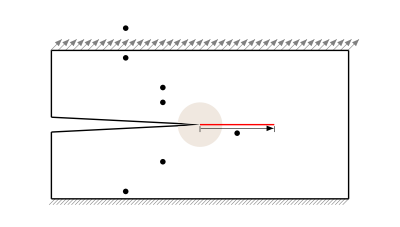

```mathematica
pt={0,0.1};
ϵ=0.01;
Graphics[{
Table[{Gray,Thickness[0.001],Line[{{p,-1},{p,-1}-{0.08,0.08}}]},{p,0.05Range[80]}],
Table[{Gray,Thickness[0.001],Arrowheads[0.01],Arrow[{{p,1},{p,1}+{0.15,0.15}}]},{p,0.1Range[-0.1,40]}],
Line[{pt,pt=pt+{0,.9}}],
Line[{pt,pt=pt+{4,0}}],
Line[{pt,pt=pt+{0,-2}}],
Line[{pt,pt=pt+{-4,0}}],
Line[{pt,pt=pt+{0,0.9}}],
Line[{pt,pt=pt+{2,0.1}}],
Line[{pt,pt=pt+{-2,0.1}}],
{LightBrown,Dashed,Disk[{2,0},.3,{-3.05646,3.05646}]},
{Red,Line[{{2,0},{3,0}}]},
{Black,Thickness[0.001],Line[{{2,-0.02},{2,-0.1}}]},
{Black,Thickness[0.001],Line[{{3,-0.02},{3,-0.1}}]},
{Black,Thickness[0.001],Arrowheads[0.01],Arrow[{{2+ϵ,-0.05},{3-ϵ,-0.05}}]},
Text[MaTeX["\\color{red}{\\hat{a}(t)}",FontSize->10,"Preamble"->{"\\usepackage{color}"}],{2.5,-0.115}],
Text[MaTeX["\\color{black}{\\Gamma^{g}}",FontSize->12,"Preamble"->{"\\usepackage{color}"}],{1,-0.9}],
Text[MaTeX["\\color{black}{\\Gamma^{h}}",FontSize->12,"Preamble"->{"\\usepackage{color}"}],{1,0.9}],
Text[MaTeX["\\color{black}{\\hat{\\boldsymbol{t}}(t)}",FontSize->12,"Preamble"->{"\\usepackage{color}"}],{1,1.3}],

Text[MaTeX["\\text{div}_{\\boldsymbol{x}}\\left(\\boldsymbol{\\sigma}(t)\\right)=\\boldsymbol{0}",FontSize->10],{1.5,0.5}],
Text[MaTeX["\\boldsymbol{\\sigma}(t)=\\hat{\\boldsymbol{\\sigma}}\\left([0,t]\\ni \\tau\\mapsto\\boldsymbol{\\epsilon}(\\tau)\\right)",FontSize->10],{1.5,0.3}],
Text[MaTeX["G(t,\\hat{a},\\hat{\\boldsymbol{t}}):=\\int_{\\Gamma^{h}}\\hat{\\boldsymbol{t}}(t)\\cdot \\dot{\\boldsymbol{u}}(t)\\, d\\Gamma^{h}-\\int_{\\Omega}\\boldsymbol{\\sigma}(t):\\dot{\\boldsymbol{\\epsilon}}(t)\\, d\\Omega",FontSize->10],{1.5,-0.5}]
},PlotRange->{{-0.2,4.2},{-1.1,1.4}}]
```

```mathematica
eq=1
```